## 1. 数据准备

### 1.1. 数据来源

Terra/Aqua卫星MODIS传感器数据反演所得的净初级生产力(NPP)逐年数据

产品MOD17A3H v006由美国地质调查局(USGS)生产和托管(DOI: 10.5067/MODIS/MOD17A3H.006)

int16类型

NPP结果单位为kg C/m.b2, 并缩小到10^-4倍

部分未计算NPP的像元根据性质被赋值32761~32767

### 1.2. 数据导入与异常值移除

时间范围: 2004年~2015年

```mathematica
ts=Import[NotebookDirectory[]<>"../Source/MOD17A3H_Lyr_Stk.tif"]//ImageData[#,"Bit16"]&//Part[#,All,All,5;;16]&//Flatten[#,1]&;
ts-=32768;
ts=DeleteCases[ts,{(_?(#>32760&))..}];
```

```mathematica
ts//Length
```

1340501

### 1.3. 训练样本选取

不放回随机抽取二十万个样本, 样本的空间分布完全随机, 抽取结果中十六万个样本被用作训练集, 四万个样本被用作测试集, 二者互斥.

```mathematica
(*Use DOI of data to initialize the random seed. *)
SeedRandom["10.5067/MODIS/MOD17A3H.006"]
tssmp=ts//RandomSample[#,200000]&;
train=tssmp[[1;;160000]];
test=tssmp[[160001;;-1]];
```

## 2. 仅考虑时间因素的回归模型

### 2.1. 利用前n年NPP预测下一年NPP

模型假设:

每个像元所在位置, 在t_(n+1)时刻的NPP值, 只和该位置t_1, t_2, …, t_n时刻的NPP值有关, 与其他像元任何时间的NPP值均无关

参与模型训练的数据规模远大于模型的复杂程度, 不需要正则化

模型建立方法

使用训练集中的最后(n+1)年至最后2年的数据作为自变量, 最后一年的数据作为因变量, 构造n元线性回归模型

```mathematica
linRegSpat//ClearAll;
linRegSpat[year_]:=linRegSpat[year]=Block[{n=year,varReg,mdlReg},
	varReg=Table[Unique["x"],{n}];
	mdlReg=train[[All,-(n+1);;-1]]//LinearModelFit[#,varReg,varReg]&;
	Return[mdlReg];
];
```

模型泛化能力测试

使用测试集中的最后(n+1)年至最后2年的数据作为自变量, 预报最后一年的数据

将预报结果与测试集中实际的数据比较, 计算RMSE

```mathematica
linRegSpatFunc//ClearAll;
linRegSpatFunc[year_]:=linRegSpatFunc[year]=linRegSpat[year]["Function"];
```

```mathematica
linRegSpatRMSE//ClearAll;
linRegSpatRMSE[year_]:=linRegSpatRMSE[year]=Block[{n=year,err,fn},
	fn=linRegSpatFunc[year];
	err=Map[(fn@@Most[#]-Last[#])&,test[[All,-(n+1);;-1]]];
	Return[err^2//Mean//Sqrt];
];
```

```mathematica
Table[linRegSpat[n]["RSquared"],{n,10}]
```

{0.847367,0.854493,0.88965,0.889749,0.898084,0.900579,0.900713,0.900967,0.90357,0.90361}

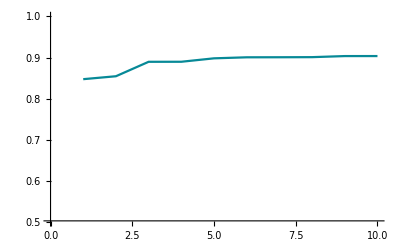

```mathematica
Table[linRegSpat[n]["RSquared"],{n,10}]//ListPlot[#,Joined->True,PlotRange->{{0, 10},{0.5,1}}]&
```

```mathematica
Table[linRegSpatRMSE[n], {n, 10}]
```

{439.268,429.473,374.372,374.164,359.811,354.913,354.61,354.315,349.69,349.541}

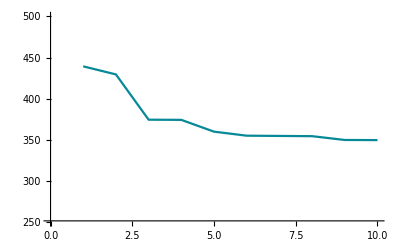

```mathematica
Table[linRegSpatRMSE[n], {n, 10}]//ListPlot[#, Joined->True, PlotRange->{{0, 10}, {250,500}}]&
```